[Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x-y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x+y/2]ⅆy];
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]-p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (-x Cos[θ]+p Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after heterodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]+s Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]);
```

#### Odd cat

```mathematica
(* ∫_(-∞)^∞ ∫_(-∞)^∞ ((ⅇ^(-((x-x2)^2+(p-p2)^2)/2))/(2π))W2mode[t,r,α,θ,x1,p1,x2,p2,s]ⅆp2ⅆx2 *)∫_(-∞)^∞ (ⅇ^(-(((x-x2)^2+(p-p2)^2)/2)))/(2π)((ⅇ^(-p1^2-p2^2-x1^2-x2^2-2  α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))-(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2
```

(ⅇ^(1/6 (-2 p^2-6 p1^2-3 x^2-6 x1^2+6 x x2-9 x2^2-12 α^2-4 √2 (p r-3 t x1) α Cos[θ]+8 r^2 α^2 Cos[θ]^2-12 √2 (p1 t+r x2) α Sin[θ])))/(√6 π^(5/2))+(ⅇ^(1/6 (-2 p^2-6 p1^2-3 x^2-6 x1^2+6 x x2-9 x2^2-12 α^2+4 √2 (p r-3 t x1) α Cos[θ]+8 r^2 α^2 Cos[θ]^2+12 √2 (p1 t+r x2) α Sin[θ])))/(√6 π^(5/2))-(ⅇ^(1/6 (-2 p^2-6 p1^2-3 x^2-6 x1^2+6 x x2-9 x2^2+12 ⅈ √2 (p1 t+r x2) α Cos[θ]-4 ⅈ √2 (p r-3 t x1) α Sin[θ]-8 r^2 α^2 Sin[θ]^2)))/(√6 π^(5/2))-(ⅇ^(1/6 (-2 p^2-6 p1^2-3 x^2-6 x1^2+6 x x2-9 x2^2-12 ⅈ √2 (p1 t+r x2) α Cos[θ]+4 ⅈ √2 (p r-3 t x1) α Sin[θ]-8 r^2 α^2 Sin[θ]^2)))/(√6 π^(5/2))

```mathematica
∫_(-∞)^∞ %ⅆx2
```

(ⅇ^(1/3 (-p^2-3 p1^2-x^2-3 x1^2-6 α^2+4 r^2 α^2-2 √2 (p r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x) α Sin[θ])))/(3 π^2)+(ⅇ^(1/3 (-p^2-3 p1^2-x^2-3 x1^2-6 α^2+4 r^2 α^2+2 √2 (p r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x) α Sin[θ])))/(3 π^2)-(ⅇ^(1/3 (-p^2-3 p1^2-x^2-3 x1^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x) α Cos[θ]-2 ⅈ √2 (p r-3 t x1) α Sin[θ])))/(3 π^2)-(ⅇ^(1/3 (-p^2-3 p1^2-x^2-3 x1^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x) α Cos[θ]+2 ⅈ √2 (p r-3 t x1) α Sin[θ])))/(3 π^2)

```mathematica
%/.{x->x2,p->p2}
```

-(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]-2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])))/(3 π^2)-(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])))/(3 π^2)+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x2) α Sin[θ])))/(3 π^2)+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x2) α Sin[θ])))/(3 π^2)

[Calc] Checking normalization

```mathematica
∫_(-∞)^∞ (-(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]-2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])))/(3 π^2)-(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])))/(3 π^2)+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x2) α Sin[θ])))/(3 π^2)+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x2) α Sin[θ])))/(3 π^2))ⅆp2
```

-(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-5 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+r^2 α^2 Cos[2 θ]-6 ⅈ √2 t x1 α Sin[θ])))/(√3 π^(3/2))-(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-5 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+r^2 α^2 Cos[2 θ]+6 ⅈ √2 t x1 α Sin[θ])))/(√3 π^(3/2))+(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-6 α^2+5 r^2 α^2+6 √2 t x1 α Cos[θ]+r^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ])))/(√3 π^(3/2))+(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-6 α^2+5 r^2 α^2-6 √2 t x1 α Cos[θ]+r^2 α^2 Cos[2 θ]+6 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ])))/(√3 π^(3/2))

```mathematica
∫_(-∞)^∞ %ⅆx2
```

(ⅇ^(-p1^2-x1^2+2 (-1+r^2) α^2+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])))/π+(ⅇ^(-p1^2-x1^2+2 (-1+r^2) α^2+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])))/π-(ⅇ^(-p1^2-x1^2-2 r^2 α^2-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))/π-(ⅇ^(-p1^2-x1^2-2 r^2 α^2+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))/π

```mathematica
∫_(-∞)^∞ %ⅆp1
```

1/(√π)ⅇ^(-x1^2-2 r^2 α^2-2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 ⅈ √2 t x1 α Sin[θ]) (-ⅇ^(2 √2 t x1 α Cos[θ])-ⅇ^(2 √2 t x1 α (Cos[θ]+2 ⅈ Sin[θ]))+ⅇ^(2 α ((-1+2 r^2+t^2) α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α ((-1+2 r^2+t^2) α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
∫_(-∞)^∞ %ⅆx1
```

2 ⅇ^(-2 (1+r^2+t^2) α^2) (-ⅇ^(2 α^2)+ⅇ^(4 (r^2+t^2) α^2))

```mathematica
%/.r^2->1-t^2
```

2 ⅇ^(-4 α^2) (-ⅇ^(2 α^2)+ⅇ^(4 α^2))

```mathematica
Simplify[%]
```

2-2 ⅇ^(-2 α^2)

[Calc] Checking normalization for Even cat

```mathematica
∫_(-∞)^∞ Wh[t,r,α,θ,x1,p1,x2,p2,1]ⅆp2
```

(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-5 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+r^2 α^2 Cos[2 θ]-6 ⅈ √2 t x1 α Sin[θ])))/(2 √3 (1+ⅇ^(-2 α^2)) π^(3/2))+(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2-5 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+r^2 α^2 Cos[2 θ]+6 ⅈ √2 t x1 α Sin[θ])))/(2 √3 (1+ⅇ^(-2 α^2)) π^(3/2))+(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2+5 r^2 α^2+6 √2 t x1 α Cos[θ]+r^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ])))/(2 √3 (1+ⅇ^(2 α^2)) π^(3/2))+(ⅇ^(1/3 (-3 p1^2-3 x1^2-x2^2+5 r^2 α^2-6 √2 t x1 α Cos[θ]+r^2 α^2 Cos[2 θ]+6 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ])))/(2 √3 (1+ⅇ^(2 α^2)) π^(3/2))

```mathematica
∫_(-∞)^∞ %ⅆx2
```

(ⅇ^(-p1^2-x1^2-2 r^2 α^2-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))/(2 π+2 ⅇ^(-2 α^2) π)+(ⅇ^(-p1^2-x1^2-2 r^2 α^2+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))/(2 π+2 ⅇ^(-2 α^2) π)+(ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])))/(2 π+2 ⅇ^(2 α^2) π)+(ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])))/(2 π+2 ⅇ^(2 α^2) π)

```mathematica
∫_(-∞)^∞ %ⅆp1
```

1/(2 (1+ⅇ^(2 α^2)) √π)ⅇ^(-x1^2-2 r^2 α^2-2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 ⅈ √2 t x1 α Sin[θ]) (ⅇ^(2 α (α+√2 t x1 Cos[θ]))+ⅇ^(2 α ((2 r^2+t^2) α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (2 r^2 α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+√2 t x1 Cos[θ]+2 ⅈ √2 t x1 Sin[θ])))

```mathematica
∫_(-∞)^∞ %ⅆx1
```

```mathematica
Cosh[(1-2 r^2-2 t^2) α^2] Sech[α^2]
```

```mathematica
%/.r^2->1-t^2
```

Cosh[(1-2 t^2-2 (1-t^2)) α^2] Sech[α^2]

```mathematica
Simplify[%]
```

1

#### s-Cat

```mathematica
(* Wh = ∫_(-∞)^∞ ∫_(-∞)^∞ ((ⅇ^(-((x-x2)^2+(p-p2)^2)/2))/(2π))W2mode[t,r,α,θ,x1,p1,x2,p2,s]ⅆp2ⅆx2 *)
Wh[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=1/(2(1+s ⅇ^(-2 α^2)))(s 1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]-2 ⅈ √2 (p2 r-3 t x1) α Sin[θ]))+s 1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+2 ⅈ √2 (p2 r-3 t x1) α Sin[θ]))+1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x2) α Sin[θ]))+1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x2) α Sin[θ])));
```

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
ClearAll[t,r,α,Δ, θ]
∫_(-Δ/2)^(Δ/2) Wh[t,r,α,θ, x1,p1,x2,p2,s]ⅆx2
```

(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-5 r^2 α^2-6 ⅈ √2 p1 t α Cos[θ]-r^2 α^2 Cos[2 θ]+2 ⅈ √2 p2 r α Sin[θ]-6 ⅈ √2 t x1 α Sin[θ])) s (-Erf[(-Δ/2+ⅈ √2 r α Cos[θ])/(√3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]))/(4 √3 π^(3/2) (1+ⅇ^(-2 α^2) s))+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-5 r^2 α^2+6 ⅈ √2 p1 t α Cos[θ]-r^2 α^2 Cos[2 θ]-2 ⅈ √2 p2 r α Sin[θ]+6 ⅈ √2 t x1 α Sin[θ])) s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]))/(4 √3 π^(3/2) (1+ⅇ^(-2 α^2) s))+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-6 α^2+5 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]-r^2 α^2 Cos[2 θ]+6 √2 p1 t α Sin[θ])) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))/(4 √3 π^(3/2) (1+ⅇ^(-2 α^2) s))+(ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-6 α^2+5 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-r^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) (-Erf[(-Δ/2+√2 r α Sin[θ])/(√3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))/(4 √3 π^(3/2) (1+ⅇ^(-2 α^2) s))

```mathematica
Simplify[%,r^2+t^2==1]
```

1/(4 √3 π^(3/2) (ⅇ^(2 α^2)+s))ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2+5 α^2-5 t^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) (ⅇ^(2/3 α (-2 α+5 t^2 α+√2 p2 r (Cos[θ]+ⅈ Sin[θ])+3 √2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ]))) s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)])+ⅇ^(2/3 α (-2 α+5 t^2 α+√2 p2 r (Cos[θ]-ⅈ Sin[θ])+3 √2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ]))) s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)])+Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]+ⅇ^(4/3 √2 α ((p2 r-3 t x1) Cos[θ]+3 p1 t Sin[θ])) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))

```mathematica
∫_(-Δp/2)^(Δp/2) (1/(4 √3 π^(3/2) (ⅇ^(2 α^2)+s))ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2+5 α^2-5 t^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) (ⅇ^(2/3 α (-2 α+5 t^2 α+√2 p2 r (Cos[θ]+ⅈ Sin[θ])+3 √2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ]))) s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)])+ⅇ^(2/3 α (-2 α+5 t^2 α+√2 p2 r (Cos[θ]-ⅈ Sin[θ])+3 √2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ]))) s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)])+Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]+ⅇ^(4/3 √2 α ((p2 r-3 t x1) Cos[θ]+3 p1 t Sin[θ])) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)])))ⅆp2
```

1/(4 √3 π^(3/2) (ⅇ^(2 α^2)+s))(-1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+4 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(-Δp/2-√2 r α Cos[θ])/(√3)] Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+4 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(Δp/2-√2 r α Cos[θ])/(√3)] Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]-1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(-Δp/2+√2 r α Cos[θ])/(√3)] Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(Δp/2+√2 r α Cos[θ])/(√3)] Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]-1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]+2/3 ⅈ α Sin[θ/2]) (-3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]-3 ⅈ √2 t x1 Sin[θ/2]+2 ⅈ α Sin[θ/2]-5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(-Δp/2-ⅈ √2 r α Sin[θ])/(√3)]-1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]+2/3 ⅈ α Sin[θ/2]) (-3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]-3 ⅈ √2 t x1 Sin[θ/2]+2 ⅈ α Sin[θ/2]-5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(-Δp/2-ⅈ √2 r α Sin[θ])/(√3)]+1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]+2/3 ⅈ α Sin[θ/2]) (-3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]-3 ⅈ √2 t x1 Sin[θ/2]+2 ⅈ α Sin[θ/2]-5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√3)]+1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]+2/3 ⅈ α Sin[θ/2]) (-3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]-3 ⅈ √2 t x1 Sin[θ/2]+2 ⅈ α Sin[θ/2]-5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√3)]-1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]-2/3 ⅈ α Sin[θ/2]) (3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]+3 ⅈ √2 t x1 Sin[θ/2]-2 ⅈ α Sin[θ/2]+5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√3)]-1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]-2/3 ⅈ α Sin[θ/2]) (3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]+3 ⅈ √2 t x1 Sin[θ/2]-2 ⅈ α Sin[θ/2]+5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√3)]+1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]-2/3 ⅈ α Sin[θ/2]) (3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]+3 ⅈ √2 t x1 Sin[θ/2]-2 ⅈ α Sin[θ/2]+5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√3)]+1/2 ⅇ^(1/3 (-r^2 α^2+r^2 α^2 Cos[2 θ])+(2/3 α Cos[θ/2]-2/3 ⅈ α Sin[θ/2]) (3 ⅈ √2 p1 t Cos[θ/2]-3 √2 t x1 Cos[θ/2]-2 α Cos[θ/2]+5 t^2 α Cos[θ/2]+3 √2 p1 t Sin[θ/2]+3 ⅈ √2 t x1 Sin[θ/2]-2 ⅈ α Sin[θ/2]+5 ⅈ t^2 α Sin[θ/2])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) s Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)] Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√3)]-1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+4 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(-Δp/2-√2 r α Cos[θ])/(√3)] Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]+1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+4 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(Δp/2-√2 r α Cos[θ])/(√3)] Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]-1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(-Δp/2+√2 r α Cos[θ])/(√3)] Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]+1/2 ⅇ^(1/3 (r^2 α^2+r^2 α^2 Cos[2 θ])+1/3 (-3 p1^2-3 x1^2+5 α^2-5 t^2 α^2+6 √2 t x1 α Cos[θ]-α^2 Cos[2 θ]+t^2 α^2 Cos[2 θ]-6 √2 p1 t α Sin[θ])) √(3 π) Erf[(Δp/2+√2 r α Cos[θ])/(√3)] Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)])

```mathematica
Simplify[%,r^2+t^2==1]
```

```mathematica
Simplify[Collect[-p1^2-x1^2+(4 α^2)/3-(4 t^2 α^2)/3+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]+2/3 α (Cos[θ/2]+ⅈ Sin[θ/2]) (-2 α Cos[θ/2]+5 t^2 α (Cos[θ/2]-ⅈ Sin[θ/2])+2 ⅈ α Sin[θ/2]+3 √2 t (p1-ⅈ x1) (-ⅈ Cos[θ/2]+Sin[θ/2])),{x1,p1}]]
```

-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
```

```mathematica
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,s_]:=(ⅇ^(-2 α^2))/(8 π (1+s ⅇ^(-2 α^2))) ((ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])+ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ])) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])(Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) +(ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])+ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]))s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)]));
```

```mathematica
ClearAll[t,r,α,θ,η,Δ,Δp,s];
expr[1]=ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]);expr[2]=ⅇ^(-p1^2-x1^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]);
expr[3]=ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]);
expr[4]=ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]);
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x1,p1}],{x1,p1}]&/@Range[4];
(w[#]={M[[#,3,1]],M[[#,1,3]],M[[#,2,1]],M[[#,1,2]],M[[#,2,2]],M[[#,1,1]]})&/@Range[4]
];
ClearAll[A,B];
subs={A->(Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])(Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]),
B->(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])};
W=(ⅇ^(-2 α^2))/(8 π (1+s ⅇ^(-2 α^2))){A,A,s B,s B}/.subs;
(* For threshold - use calcs from Wigner Cat -v2.nb and iPad: Cat via noisy Threshold ZPS *)
ClearAll[V,Vfunc,v];
Vfunc[μ_,s_]:=(ⅇ^(t^2 α^2))/(2π)s^μ((Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2])/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2))));
V[s_]:={Vfunc[0,s],Vfunc[0,s],Vfunc[1,s],Vfunc[1,s]};
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) *)
v[1]=-{-1,-1,2 √2 t  α Cos[θ],-2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) *)
v[2]=-{-1,-1,-2 √2 t α Cos[θ],2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) *)
v[3]=-{-1,-1,2 ⅈ √2 t  α Sin[θ],+2 ⅈ √2 t α Cos[θ],0,0};
(* ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) *)
v[4]=-{-1,-1,-2 ⅈ √2 t α Sin[θ],-2 ⅈ √2 t α Cos[θ],0,0};
(* Gaussian integrals *)
int[v_,w_]:=integral@@ (v~Join~w);
(*∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-(A11 x^2+ A21 p^2+B11 x +B21 p +B121 x p +C1))ⅇ^(-(A12 x^2+ A22 p^2+B12 x +B22 p +B122 x p +C2))ⅆxⅆp*)
integral[A11_, A21_ ,B11_ ,B21_ ,B121_ , C1_,A12_, A22_ ,B12_ ,B22_ ,B122_ , C2_]:=(2 ⅇ^((-B11 B121 B21-B12 B121 B21-B11 B122 B21-B12 B122 B21+A11 B21^2+A12 B21^2-B11 B121 B22-B12 B121 B22-B11 B122 B22-B12 B122 B22+2 A11 B21 B22+2 A12 B21 B22+A11 B22^2+A12 B22^2+B121^2 C1+2 B121 B122 C1+B122^2 C1+(B121+B122)^2 C2+A21 ((B11+B12)^2-4 (A11+A12) (C1+C2))+A22 ((B11+B12)^2-4 (A11+A12) (C1+C2)))/(4 (A11+A12) (A21+A22)-(B121+B122)^2)) π)/(√(4 (A11+A12) (A21+A22)-(B121+B122)^2));(*ConditionalExpression[(2 ⅇ^((B11^2+2 B11 B12+B12^2+(B11 (B121+B122)+B12 (B121+B122)-2 (A11+A12) (B21+B22))^2/(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)-4 A11 C1-4 A12 C1-4 A11 C2-4 A12 C2)/(4 (A11+A12))) π)/(√(A11+A12) √((4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)/(A11+A12))), Re[(-4 A11 (A21+A22)-4 A12 (A21+A22)+(B121+B122)^2)/(A11+A12)]≤0];*)
```

```mathematica
(* Probability of success *)
∫_(-∞)^∞ ∫_(-∞)^∞ (WunnormHetero[t,r,α,θ,x1,p1,Δ,Δp,s])ⅆx1ⅆp1
```

1/(4 (ⅇ^(2 α^2)+s))(s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2/3 (2+r^2+t^2) α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))

```mathematica
Simplify[%,r^2+t^2==1]
```

1/(4 (ⅇ^(2 α^2)+s))(s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))

[Rslt] Wigner distributions - essential code (General cat)

```mathematica
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,s_]:= (ⅇ^(-2 α^2))/(8 π (1+s ⅇ^(-2 α^2))) ((ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])+ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ])) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])(Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) +(ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])+ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]))s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)]));PsHetero[t_,r_,α_,θ_,Δx_,Δp_,s_]:= (ⅇ^(-2 α^2))/(4 (1+s ⅇ^(-2 α^2)))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)]));

WnHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,s_]:=Re[WunHetero[t,r,α,θ,x1,p1,Δx,Δp,s]/PsHetero[t,r,α,θ,Δx,Δp,s]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
(* Results for the threshold detectors obtained from iPad *)

WnThreshold[t_,α_,θ_,x1_,p1_,η_,s_]:=((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2]Wcat[t α,θ,x1,p1,-1]+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2]Wcat[t α,θ,x1,p1,1];
PsThreshold[t_,α_,η_,s_]:=(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))])/(Exp[α^2]+s Exp[-α^2]);
PsηRelativeImprovement[t_,r_,α_,θ_,Δ_,Δp_,η_,s_]:=Re[(PsHetero[t,r,α,θ,Δ,Δp,s]-PsThreshold[t,α,η,s])/PsThreshold[t,α,η,s]];
(*
Fidelity:
(2π)/PsHetero[t,r,α,θ,Δ,Δp,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]int[v[i],w[j]];

ηPurity:
2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]int[v[i],v[j]];

*)
ηPurity[t_,r_,α_,θ_,η_,s_]:=(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2);
```

```mathematica
FullSimplify[(((2π)/PsHetero[t,r,α,θ,Δx,Δp,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]Simplify[int[v[i],w[j]]])/.{Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)]->Ax, Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]->Ap,Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)] ->Bx,Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)]->Bp})/.{Ap Ax->A,Bp Bx->B},r^2+t^2==1]
```

(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (A (ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s)+B s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s)))/(2 (A ⅇ^(2 α^2)+B s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s))

```mathematica
((ⅇ^(-2 α^2 (1+(-1+t^2) η)) (A (ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s)+B s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s)))/(2 (A ⅇ^(2 α^2)+B s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s)))/.subs
```

(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])))

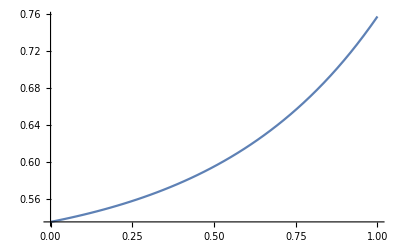

```mathematica
Fidelity[t_,r_,α_,θ_,Δx_,Δp_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √3)])));
Plot[Fidelity[√0.75,√0.25,2,0,.1,0.1,η,1],{η,0,1},PlotRange->All]
```

```mathematica
(* For comparing two Wigner distributions *)
(* Relative Overlap *)
ηRelativeOverlap[t_,r_,α_,θ_,Δx_,Δp_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-Fidelity[t,r,α,θ,Δx,Δp,η,s];
```

```mathematica
Simplify[lim_(Δ->0^+) (ηRelativeOverlap[t,r,α,θ,Δ,Δ,η,s]),r^2==1-t^2]
```

(ⅇ^(-2/3 α^2 (3+t^2 (8+6 η))) (-1+ⅇ^(4 t^2 α^2)) (ⅇ^(2/3 α^2 (2 t^2+3 η))-ⅇ^(2/3 α^2 (2+3 t^2 η))) s (ⅇ^(2 α^2 (1+t^2 η))+ⅇ^(2 α^2 (2 t^2+η)) s))/(2 (ⅇ^(2 α^2)+ⅇ^((4 r^2 α^2)/3) s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)

```mathematica
LimitingFunction[t_,r_,α_,θ_,η_,s_]:=Re[(ⅇ^(-2/3 α^2 (3+t^2 (8+6 η))) (-1+ⅇ^(4 t^2 α^2)) (ⅇ^(2/3 α^2 (2 t^2+3 η))-ⅇ^(2/3 α^2 (2+3 t^2 η))) s (ⅇ^(2 α^2 (1+t^2 η))+ⅇ^(2 α^2 (2 t^2+η)) s))/(2 (ⅇ^(2 α^2)+ⅇ^((4 r^2 α^2)/3) s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)];
ηmax[t_,r_,α_,θ_,s_]:=FindRoot[LimitingFunction[t,r,α,θ,η,s],{η,1}];
```

[Rslt] Comparisons

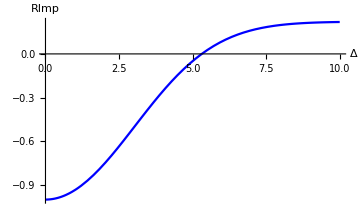

```mathematica
Plot[PsηRelativeImprovement[√0.75,√0.25,2,0,Δ,Δ,0.2,1],{Δ,0,10},AxesLabel->{Δ,RImp},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

```mathematica
ηmax[√0.75,√0.25,2,0,1]
```

{η→0.666667}

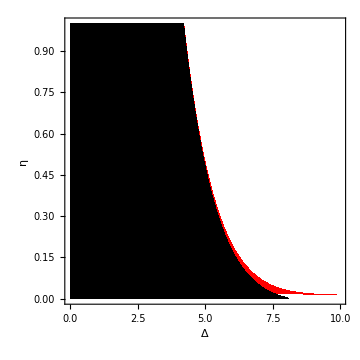

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that heterodyning is better to simulate certain efficiencies. Observation: α needs to be sufficienctly small. But be wary that too small α means we need bigger Δ. *)
α=1.1;plotRO = DensityPlot[HeavisideTheta[Re[ηRelativeOverlap[√0.75,√0.25,α,0,Δ,Δ,η,1]]],{Δ,0,10},{η,0,1},PlotPoints->60,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRI=DensityPlot[HeavisideTheta[PsηRelativeImprovement[√0.75,√0.25,α,0,Δ,Δ,η,1]],{Δ,0,10},{η,0,1},PlotPoints->60,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotRO,plotRI}]
ClearAll[α];
```

```mathematica
(* Numerically fnding the point where Threshold and Heterodyne detections are equivalent, i.e. where RO(η,Δ)==0 AND RI(η,Δ)==0 *)
```

```mathematica
EquivalencePoint[t_,r_,α_,θ_]:=FindRoot[{ηRelativeOverlap[t,r,α,θ,Δ,Δ,η,1]==0,PsηRelativeImprovement[t,r,α,θ,Δ,Δ,η,1]==0},{{η,1},{Δ,1}}];
```

```mathematica
ClearAll[list,arg];
list[t_,θ_,αmin_,αmax_,dα_]:=({η,#,Δ}/.EquivalencePoint[t,√(1-t^2),#,θ])&/@Range[αmin,αmax,dα];
Quiet[arg=list[#,0,1,2,0.01]&/@Range[√0.5,1,0.001];]
```

$Aborted

```mathematica
plotlist=ListPointPlot3D[arg[[#]],PlotRange->{{0,1},Automatic,Automatic},AxesLabel->{η,α,Δ},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->RGBColor[0,0,1-#/(Dimensions[arg][[1]]),1-0.8#/(Dimensions[arg][[1]])]]&/@Range[Dimensions[arg][[1]]];
```

```mathematica
Show[plotlist]
```

-Graphics3D-

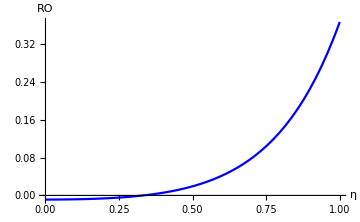

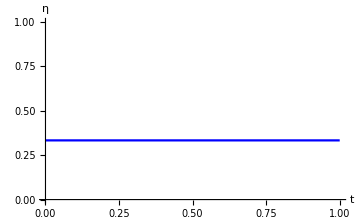

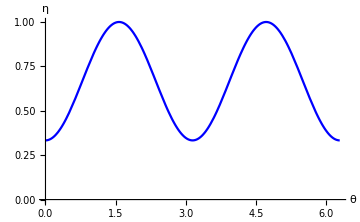

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

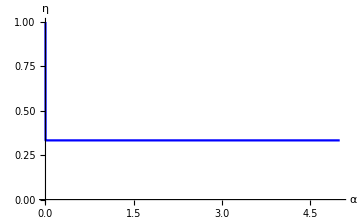

```mathematica
(* Limiting function assuming lim Δ->0^+ gives ηmax. Not true as there could be some minimum Δ beyond which there is a solution. For example see the case of α = 1.2. It doesn't start at Δ=0.s *)
Plot[LimitingFunction[√0.75,√0.25,2,0,η,1],{η,0,1},AxesLabel->{η,RO},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full]
(* Behavior with beamsplitter trasmittivity starts at √0.5 *)
Plot[η/.ηmax[√T,√(1-T),2,0,1],{T,0,1},PlotRange->{0,1},AxesLabel->{t,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
(* Behavior with θ *)
Plot[η/.ηmax[√0.75,√0.25,2,θ,1],{θ,0,2π},PlotRange->{0,1},AxesLabel->{θ,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
(* Behavior with α *)
Plot[η/.ηmax[√0.75,√0.25,α,0,1],{α,0,5},PlotRange->{0,1},AxesLabel->{α,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
(* There are several unphysical parameter spaces one needs to be wary about *)
```

```mathematica
η/.ηmax[√0.75,√(1-0.75),2,0,1]
```

0.333333

Fixing Δ finding η

```mathematica
WnHetero[√0.75,√0.25,2,0,0,0,2,2,1]
```

0.125279

Heterodyne success probability:

0.00253249

{η→0.667894}

Threshold success probability:

0.264138

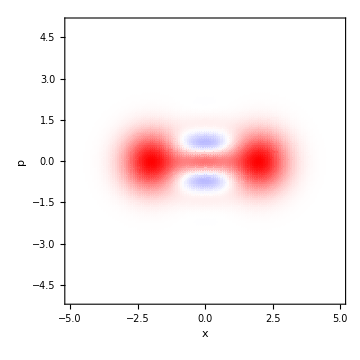
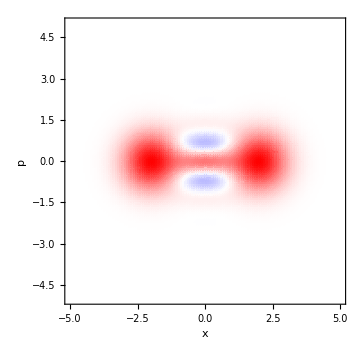
(a) Threshold | (b) Heterodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δ,Δp,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ=0;
s=1; (* s-cat *)
Δ=Δp=0.3;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);

(* Psuccess *)
"Heterodyne success probability: "
Re[PsHetero[t,r,α,θ,Δ,Δp,s]]


matWnHetero=Table[Re[Chop[WnHetero[t,r,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ,Δp,s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHetero =matWnHetero/(Abs[ Total[matWnHetero,2]](limits/range)^2);

(*model=WnThreshold[t,α,θ,x,p,η,s];
range =(Dimensions[matWnHetero ][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWnHetero [[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]*)
fit =ηmax[t,r,α,θ,s]

matWnThreshold=Table[Re[Chop[WnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit,s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnThreshold=matWnThreshold/(Abs[Total[matWnThreshold,2]](limits/range)^2);
"Threshold success probability: "
PsThreshold[t,α,η/.fit,s]

plotThreshold=ListDensityPlot[matWnThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnThreshold]],Abs[Min[matWnThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHeterodyne=ListDensityPlot[matWnHetero,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnHetero]],Abs[Min[matWnHetero]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Heterodyne"},{plotThreshold,plotHeterodyne}}]
```

Comparing P_S for odd cat states w.r.t. θ

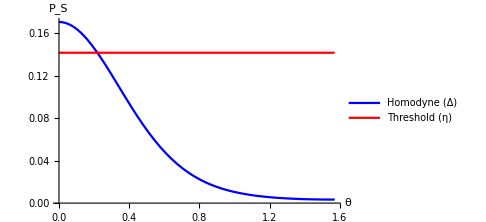

```mathematica
Plot[{Ps[t,√(1-t^2),α,θ,Δ], PsThreshold[t,α,η/.fit]},{θ,0,π/2},AxesLabel->{θ,Subscript[P, S]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->{"Homodyne (Δ)","Threshold (η)"}]
```